```mathematica
g = 9.81;
```

```mathematica
tmax = 10;
```

```mathematica
reflected = ReflectionTransform[{-x[t], -y[t]}][{x'[t], y'[t]}];
```

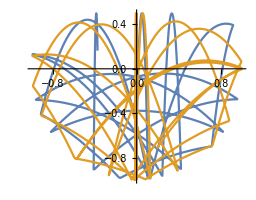

```mathematica
solveSystem[x0_, y0_]:= NDSolveValue[
{
y''[t]== -g,
x''[t]== 0,
x'[0]== 0,
y'[0] ==  0,
x[0]== x0,
y[0]== y0,
WhenEvent[x[t]^2+y[t]^2 == 1,
{x'[t],y'[t]}-> Evaluate[reflected]
]
},
{x,y},
{t,0,tmax}
];
{xf1, yf1}=solveSystem[0.001, 0.5];
{xf2, yf2}=solveSystem[0.0012, 0.5];

ParametricPlot[{{xf1[t], yf1[t]},{xf2[t], yf2[t]}}, {t,0,tmax}]
```

```mathematica
col1=RGBColor[1.,0.7,0.29];
col2 = RGBColor[0.,0.86, 0.9];
colbg = RGBColor[0., 0.07,0.15];
frame[tt_]:=Show[
Graphics[{
White,
AbsoluteThickness[2],
Circle[{0,0}, 1.05]
},
PlotRange->1.2,
Background->colbg
],
ListPlot[{{xf1[tt],yf1[tt]}, {xf2[tt],yf2[tt]}},PlotStyle->{col1,col2},AspectRatio->1,PlotMarkers->{Automatic, Medium}],
ParametricPlot[{{xf1[t],yf1[t]}, {xf2[t],yf2[t]}}, {t,0,tt +0.001}]
];
```

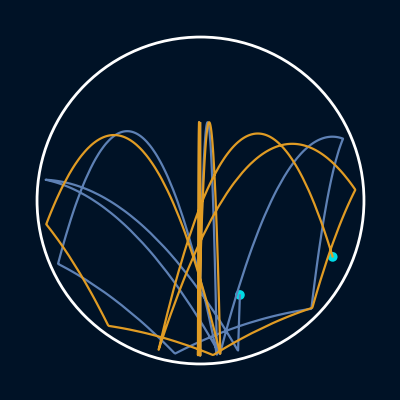

```mathematica
frame[6]
```

```mathematica
balls =Table[frame[t],{t,0,8, 0.05}];
```

```mathematica
Export["balls_col.gif", balls,"DisplayDurations"->0.01]
```

balls_col.gif